# Diagonalización Exacta: Modelo Bose - Hubbard

## Novoa Gastaldi Alejandro Silvestre

(silvestre.novoa@ciencias.unam.mx)

## 03/2019

```mathematica
Clear["Global`*"]
```

#### N = 4 Partículas. M = 4 Sitios

Comparación de los Valores de Tags en la Base con orden Lexicografico respecto al orden de Tag Ascendente

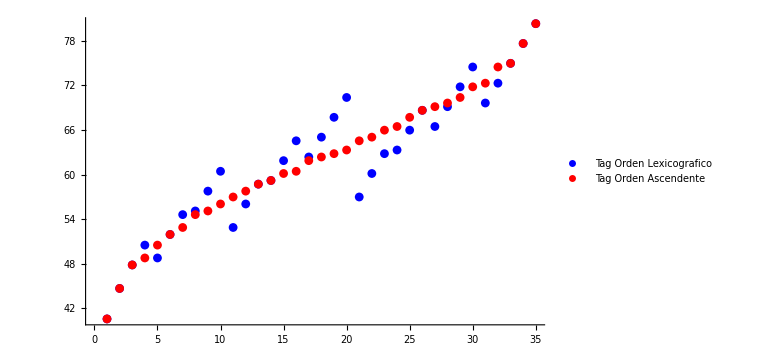

Hamiltoniano con Orden Lexicografico

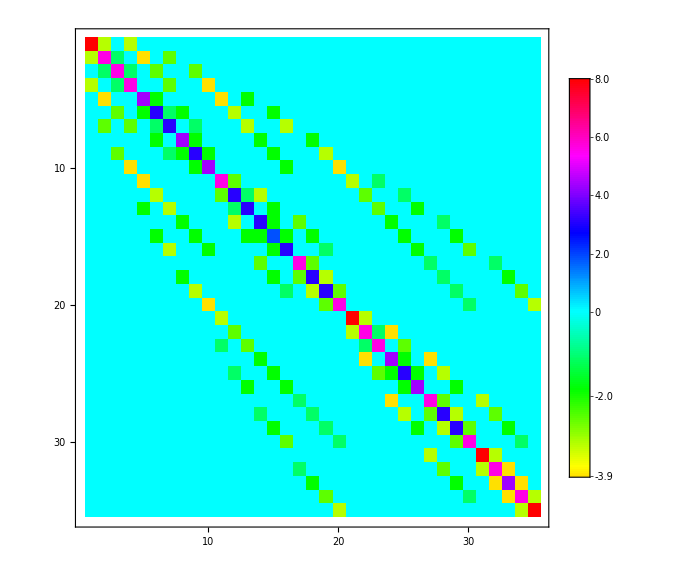

Hamiltoniano con Orden de Tag Ascendente

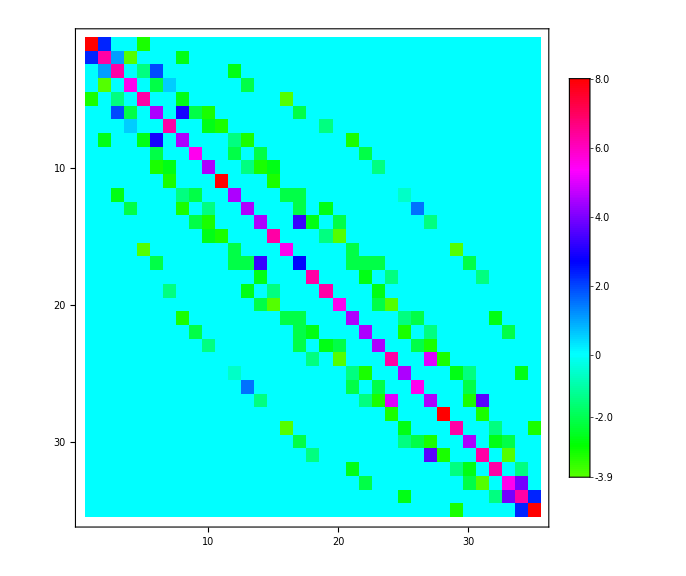

Energía del Estado Base

(0.004 | -1.99898
0.008 | -1.99589
0.012 | -1.99073
0.016 | -1.98345
0.02 | -1.97401
0.024 | -1.96235
0.028 | -1.94842
0.032 | -1.93215
0.036 | -1.91351
0.04 | -1.89246
0.044 | -1.86898
0.048 | -1.8431
0.052 | -1.81484
0.056 | -1.78426
0.06 | -1.75146
0.064 | -1.71653
0.068 | -1.67959
0.072 | -1.64076
0.076 | -1.60019
0.08 | -1.55801
0.084 | -1.51433
0.088 | -1.4693
0.092 | -1.42302
0.096 | -1.3756
0.1 | -1.32715
0.104 | -1.27775
0.108 | -1.22749
0.112 | -1.17644
0.116 | -1.12467
0.12 | -1.07225
0.124 | -1.01922
0.128 | -0.965632
0.132 | -0.911535
0.136 | -0.856966
0.14 | -0.801962
0.144 | -0.746554
0.148 | -0.690771
0.152 | -0.63464
0.156 | -0.578185
0.16 | -0.521428
0.164 | -0.464387
0.168 | -0.407082
0.172 | -0.349528
0.176 | -0.291741
0.18 | -0.233734
0.184 | -0.175521
0.188 | -0.117112
0.192 | -0.0585186
0.196 | 0.00024932
0.2 | 0.0591827
0.204 | 0.118273
0.208 | 0.177512
0.212 | 0.236893
0.216 | 0.296409
0.22 | 0.356053
0.224 | 0.415819
0.228 | 0.475702
0.232 | 0.535697
0.236 | 0.595799
0.24 | 0.656003
0.244 | 0.716305
0.248 | 0.776701
0.252 | 0.837186
0.256 | 0.897758
0.26 | 0.958413
0.264 | 1.01915
0.268 | 1.07996
0.272 | 1.14085
0.276 | 1.2018
0.28 | 1.26283
0.284 | 1.32392
0.288 | 1.38507
0.292 | 1.44629
0.296 | 1.50756
0.3 | 1.5689
0.304 | 1.63029
0.308 | 1.69173
0.312 | 1.75322
0.316 | 1.81477
0.32 | 1.87636
0.324 | 1.938
0.328 | 1.99969
0.332 | 2.06142
0.336 | 2.12319
0.34 | 2.18501
0.344 | 2.24686
0.348 | 2.30876
0.352 | 2.37069
0.356 | 2.43266
0.36 | 2.49467
0.364 | 2.55671
0.368 | 2.61878
0.372 | 2.68089
0.376 | 2.74303
0.38 | 2.8052
0.384 | 2.86741
0.388 | 2.92964
0.392 | 2.9919
0.396 | 3.05419
0.4 | 3.11651
0.404 | 3.17885
0.408 | 3.24122
0.412 | 3.30362
0.416 | 3.36604
0.42 | 3.42849
0.424 | 3.49096
0.428 | 3.55345
0.432 | 3.61596
0.436 | 3.6785
0.44 | 3.74106
0.444 | 3.80364
0.448 | 3.86624
0.452 | 3.92886
0.456 | 3.9915
0.46 | 4.05416
0.464 | 4.11684
0.468 | 4.17954
0.472 | 4.24225
0.476 | 4.30498
0.48 | 4.36773
0.484 | 4.4305
0.488 | 4.49329
0.492 | 4.55609
0.496 | 4.6189
0.5 | 4.68173
0.504 | 4.74458
0.508 | 4.80744
0.512 | 4.87032
0.516 | 4.93321
0.52 | 4.99611
0.524 | 5.05903
0.528 | 5.12197
0.532 | 5.18491
0.536 | 5.24787
0.54 | 5.31084
0.544 | 5.37383
0.548 | 5.43682
0.552 | 5.49983
0.556 | 5.56285
0.56 | 5.62588
0.564 | 5.68893
0.568 | 5.75198
0.572 | 5.81505
0.576 | 5.87812
0.58 | 5.94121
0.584 | 6.00431
0.588 | 6.06742
0.592 | 6.13054
0.596 | 6.19366
0.6 | 6.2568
0.604 | 6.31995
0.608 | 6.3831
0.612 | 6.44627
0.616 | 6.50945
0.62 | 6.57263
0.624 | 6.63582
0.628 | 6.69902
0.632 | 6.76223
0.636 | 6.82545
0.64 | 6.88868
0.644 | 6.95192
0.648 | 7.01516
0.652 | 7.07841
0.656 | 7.14167
0.66 | 7.20493
0.664 | 7.26821
0.668 | 7.33149
0.672 | 7.39478
0.676 | 7.45807
0.68 | 7.52137
0.684 | 7.58468
0.688 | 7.648
0.692 | 7.71132
0.696 | 7.77465
0.7 | 7.83799
0.704 | 7.90133
0.708 | 7.96468
0.712 | 8.02803
0.716 | 8.0914
0.72 | 8.15476
0.724 | 8.21814
0.728 | 8.28152
0.732 | 8.3449
0.736 | 8.40829
0.74 | 8.47169
0.744 | 8.53509
0.748 | 8.5985
0.752 | 8.66191
0.756 | 8.72533
0.76 | 8.78875
0.764 | 8.85218
0.768 | 8.91561
0.772 | 8.97905
0.776 | 9.0425
0.78 | 9.10595
0.784 | 9.1694
0.788 | 9.23286
0.792 | 9.29632
0.796 | 9.35979
0.8 | 9.42326)

Fluctuaciones  Δ(n_i)^2

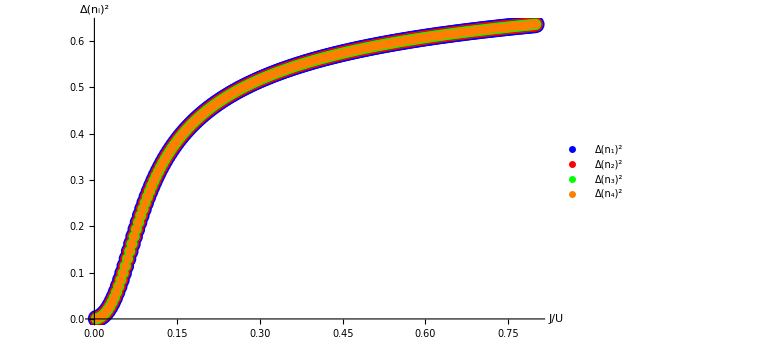

Matriz de Densidad Reducida  ρ. Su traza es igual al numero de partículas

4.

(1. | 0.549667 | 0.447356 | 0.446955
0.549667 | 1. | 0.588224 | 0.575713
0.447356 | 0.588224 | 1. | 0.634064
0.446955 | 0.575713 | 0.634064 | 1.)

Fracción de Condensado  f_c

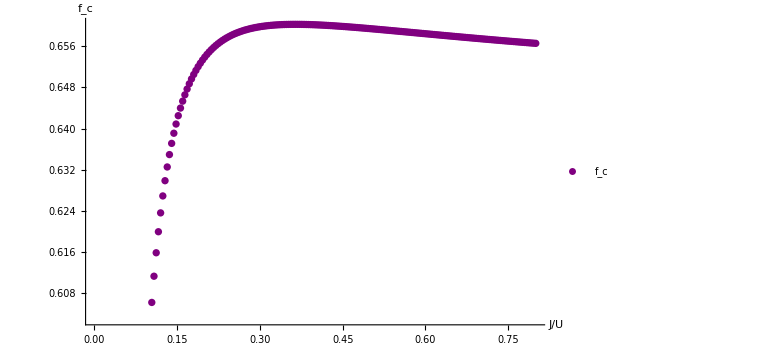

```mathematica
Clear["Global`*"]

(********************* ----- SISTEMA ----- *********************)


(* Se plantea un sistema de M sitios con N Particulas *)

NParticulas=4;
MSitios=4;
NTotalEstados=(NParticulas+MSitios-1)!/((NParticulas)!*(MSitios-1)!);   (*Numero Total de Estados que constituyen la base del espacio de Hilbert *)


(*Parametros*)
U=1.;
t0=0.004;

NPuntos=200.;
t=Table[t0*i,{i,1,NPuntos}];

(*Valores por determinar dentro de las iteraciones*)
EnergiaEdoBase  = Table[ {t[[lk]]    ,     0      }, {lk,1,NPuntos}];   
Dn2  = Table[ {t[[lk]]    ,     0      }, {lk,1,NPuntos}]; 
FraccionCondensado = Table[ {t[[lk]]    ,     0      }, {lk,1,NPuntos}];   




(********************* ----- GENERACIÓN BASE CON ORDEN LEXICOGRAFICO ----- *********************)


(*Funciones para la generación de la base*)
Generadorkn[x_,y_]:=Module[{MSitios=x,in=y},{i=MSitios-1,While[B[[in,i]]==0,i--],kn=i}];       (* Funcion que genera el valor kn de un estado B[[ in ]] para contruir el estado B[[ in+1 ]] *)

GeneradorElemento[x_,y_,z_]:=Module[{MSitios=x,in=y,k=z},{For[i=1,i<k,i++,B[[in+1,i]]=B[[in,i]]],For[i=k,i<k+1,i++,B[[in+1,i]]=B[[in,i]]-1], For[i=k+1,i<k+2,i++,B[[in+1,i]]=NParticulas-Sum[B[[in+1,j]],{j,1,i,1}]],
For[i=k+2,i<MSitios,i++,B[[in+1,i]]=0]}];       (* Funcion que genera el estado B[[ in+1 ]] a partir de el valor kn y del estado B[[ in ]] *)

GeneradorBase[x_,y_]:=Module[{MSitios=x,NTotalEstados=y},Do[{Generadorkn[MSitios,j],GeneradorElemento[MSitios,j,kn]},{j,1,NTotalEstados-1,1}]];  (* Se juntan las dos funciones anteriores iterandolas en un Do, partiendo de un estado inicial para contruir toda la base con orden Lexicografico *)



(***** Se Genera la Base *****)

B=Table[Table[0,{i,1,MSitios}],{i,1,NTotalEstados}];
B[[1,1]]=NParticulas;

GeneradorBase[MSitios,NTotalEstados];
MatrixForm[B];






(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)






(********************* ----- GENERACIÓN DEL TAG-BASE CON ORDEN ASCENDENTE ----- *********************)


TagBase=Table[0,{i,1,NTotalEstados}];
Do[TagBase[[j]]=Sum[Sqrt[100*i+3]*B[[j,i]],{i,1,MSitios,1}],{j,1,NTotalEstados,1}];       (* Se crea un tag para cada estado base a partir de numeros (etiquetas) irrepetibles contruidos por el numero de particulas en cada sitio para cada estado de la base *)
TagBaseOrdenada=Sort[TagBase,#1<#2&];   (* Se ordena de Forma Ascendente *)






(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)




(*ITERACIÓN RESPECTO A t*)
Do[

(********************* ----- HAMILTONIANO CON ORDEN LEXICOGRAFICO ----- *********************)


HBbase=Table[Table[0,{i,1,NTotalEstados,1}],{j,1,NTotalEstados,1}];


(* Terminos No Diagonales *)

Do[{
(*Genero los Operadores como vectores que suman la unidad en un sitio y lo quitan en otro*)
Operador  =  Join[    Table[   UnitVector[MSitios,  Mod[i,MSitios,1]  ]  -   UnitVector[MSitios,  Mod[i+1,MSitios,1]  ],{i,1,MSitios,1}]    ,    Table[  -  UnitVector[MSitios,  Mod[i,MSitios,1]  ]  +   UnitVector[MSitios,  Mod[i+1,MSitios,1]  ],{i,1,MSitios,1}]    ]          ;

(*Aplico cada Operador a un estado*)
EdoOperado  =  Table[  B[[  ln  ]]  +  Operador[[i]]  ,  {i,1,2*MSitios,1} ]          ;

(*Calculo el Tag del estado resultante de cada operación *)
TagEdoOperado  =  Table[  Sum[  Sqrt[  100*i+3  ]  *  EdoOperado[[j,i]]  ,  {i,1,MSitios,1}]  ,  {j,1,2*MSitios,1} ]          ;

(*Calculo el coeficiente asociado a cada operación. El coeficiente esta es el respectivo a los operadores de creación y aniquilación*)
CoefOperador  =  Join[    Table[    Sqrt[  B[[   ln   ,Mod[i,MSitios,1]  ]]  +  1  ]  *  Sqrt[  B[[  ln   ,Mod[i+1,MSitios,1]  ]]  ],{ i,1,MSitios,1}]    ,     Table[        Sqrt[  B[[  ln   ,Mod[i,MSitios,1]  ]]  ]  *   Sqrt[  B[[   ln   ,Mod[i+1,MSitios,1]  ]]  +  1  ] ,{ i,1,MSitios,1}]     ]          ;

(* Identifico la posición del estado resultante de la operación en la Base. Teniendo esto, puedo asignarle el coeficiente a la entrada que corresponde del hamiltoniano *)
Do[   HBbase[[  ln  ,   Flatten[Position[TagBase,TagEdoOperado[[i]]  ]]   ]]      =    HBbase[[  ln  ,   Flatten[Position[TagBase,TagEdoOperado[[i]]  ]]   ]]    +    CoefOperador[[i]]    , {i,1,2*MSitios,1}  ]        },

(*Se itera para todos los estados*)
                                            {ln,1,NTotalEstados,1}];


HBbase  =-t[[     itn    ]]*(HBbase+ConjugateTranspose[HBbase]);    


(* Terminos de la Diagonal *)

HBbaseDiagonal=Table[   Sum[  B[[j,i]]^2  ,{i,1,MSitios,1}  ]  ,{j,1,NTotalEstados}];      (*Respectivo al operador de numero al cuadrado*)

Do[HBbase[[i,i]]=U*HBbaseDiagonal[[i]]/2,{i,1,NTotalEstados}];



HBbase // MatrixForm;







(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)








(********************* ----- HAMILTONIANO CON ORDEN TAG ASCENDENTE ----- *********************)


HTAGbase=Table[Table[0,{i,1,NTotalEstados,1}],{j,1,NTotalEstados,1}];


(*Genero Base REORDENADA respecto al ordenamiento del Tag*)
BOrdenTag=Table[  { TagBase[[j]]  ,  B[[j]]  }  ,{j,1,NTotalEstados}];
BOrdenTag =Sort[  BOrdenTag  ,#1[[1]]<#2[[1]]&] ;       (*Reordena respecto a la primer entrada de los vectores. De menor a mayor*)
BOrdenTag =BOrdenTag[[1;;NTotalEstados,2]];



(* Terminos No Diagonales *)

Do[{
(*Genero los Operadores como vectores que suman la unidad en un sitio y lo quitan en otro*)
Operador  =  Join[    Table[   UnitVector[MSitios,  Mod[i,MSitios,1]  ]  -   UnitVector[MSitios,  Mod[i+1,MSitios,1]  ]     ,{i,1,MSitios,1}]    ,    Table[  -  UnitVector[MSitios,  Mod[i,MSitios,1]  ]  +   UnitVector[MSitios,  Mod[i+1,MSitios,1]  ]     ,{i,1,MSitios,1}]    ]          ;

(*Aplico cada Operador a un estado*)
EdoOperado  =  Table[  BOrdenTag[[  ln  ]]  +  Operador[[i]]  ,  {i,1,2*MSitios,1} ]          ;

(*Calculo el Tag del estado resultante de cada operación *)
TagEdoOperado  =  Table[  Sum[  Sqrt[  100*i+3  ]  *  EdoOperado[[j,i]]  ,  {i,1,MSitios,1}]  ,  {j,1,2*MSitios,1} ]          ;

(*Calculo el coeficiente asociado a cada operación. El coeficiente esta es el respectivo a los operadores de creación y aniquilación*)
CoefOperador  =  Join[    Table[    Sqrt[  BOrdenTag[[   ln   ,Mod[i,MSitios,1]  ]]  +  1  ]  *  Sqrt[  BOrdenTag[[  ln   ,Mod[i+1,MSitios,1]  ]]  ],{ i,1,MSitios,1}]    ,     Table[        Sqrt[  BOrdenTag[[  ln   ,Mod[i,MSitios,1]  ]]  ]  *   Sqrt[  BOrdenTag[[   ln   ,Mod[i+1,MSitios,1]  ]]  +  1  ] ,{ i,1,MSitios,1}]     ]          ;

(* Identifico la posición del estado resultante de la operación en la Base. Teniendo esto, puedo asignarle el coeficiente a la entrada que corresponde del hamiltoniano *)
Do[   HTAGbase[[  ln  ,   Flatten[Position[TagBaseOrdenada,TagEdoOperado[[i]]  ]]   ]]      =    HBbase[[  ln  ,   Flatten[Position[TagBaseOrdenada,TagEdoOperado[[i]]  ]]   ]]    +    CoefOperador[[i]]    , {i,1,2*MSitios,1}  ]        },

(*Se itera para todos los estados*)
                                            {ln,1,NTotalEstados,1}];


HTAGbase  =-t[[     NPuntos    ]] * (HTAGbase+ConjugateTranspose[HTAGbase]);

(* Terminos de la Diagonal *)

Do[HTAGbase[[i,i]]=  U  *   Sum[  BOrdenTag[[i,j]]^2  ,  {j,1,MSitios,1}  ]  /2  ,{i,1,NTotalEstados}];       (*Respectivo al operador de numero al cuadrado*)




HTAGbase // MatrixForm;







(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)







(********************* ----- OBSERVABLES ----- *********************)





(******* ESTADO BASE *******) 



EnergiaEdoBase[[     itn     ,2]]= Eigensystem[-HBbase,1,Method->{"Arnoldi","Criteria"->"RealPart"}][[1]] -  0*U*NParticulas/2 ;      (* Se resta el termino constante del Hamiltoniano *)



EdoBase=Flatten[    Eigensystem[  -HBbase,1,Method->{"Arnoldi","Criteria"->"RealPart"}  ][[2]]    ];





(******* FLUCTUACIONES *******) 


(*La varianza del operador de numero por sitio respecto al estado Base*)

Dn2 [[     itn     , 2 ]] =   Table[      Sum[    B[[i,j]]^2  *  EdoBase[[i]]*  Conjugate[ EdoBase[[i]] ]    ,{i,1,NTotalEstados,1}   ]   -   Sum[    B[[i,j]]  *  EdoBase[[i]]*  Conjugate[ EdoBase[[i]] ]    ,{i,1,NTotalEstados,1}   ]^2    , {j,1,MSitios,1} ];






(******* MATRIZ DE DENSIDAD REDUCIDA *******) 


Mρ=Table[Table[0,{i,1,MSitios,1}],{j,1,MSitios,1}];


(* Terminos No Diagonales *)

(* Operadores y los indices de su entrada correspondiente: Se definen los operadores como vectores para ser sumados al estado sobre el cual actuan. 
Cada operador va a estar asociado a una entrada especifica de la matriz, se considera las entradas de los elementos superiores a la diagonal.*)
Operador  =   Flatten[      Table[  Table[   UnitVector[MSitios,  Mod[j,MSitios,1]  ]  -   UnitVector[MSitios,  Mod[i+j,MSitios,1]  ]     ,{i,1,MSitios-j,1}  ] ,{j,1,MSitios-1,1}   ]    ,1  ]    ;
IndiceFila = Flatten[  Table[   Table[   j  ,{i,j,MSitios-1,1}]   ,{j,1,MSitios-1,1}]  ];
IndiceColumna = Flatten[  Table[   Table[   i  ,{i,j,MSitios,1}]   ,{j,2,MSitios,1}]  ];



Do[    {   

CoefOperadorMρ =Table[0,{i,1,NTotalEstados,1}];

Do[    {

(*Se aplica el operador*)
EdoOperado  =    B[[  ln  ]]  +  Operador [[jn]]     ;

(* Calculo el Tag del estado resultante de cada operación *)
TagEdoOperado  =    Sum[  Sqrt[  100*i+3  ]  *  EdoOperado[[i]]  ,  {i,1,MSitios,1}]    ;

(* Calculo el coeficiente asociado a cada operación. El coeficiente esta es el respectivo a los operadores de creación y aniquilación, PERO ESTA MULTIPLICADO POR EL COEFICIENTE DEL ESTADO PREVIO A SER OPERADO, POR EL COEFICIENTE ASOCIADO AL ESTADO RESULTANTE DE LA OPERACIÓN, i.e., C_{i} * C_{k} donde k es determinado comparando el TAG del EDO OPERADO con la base ordenada, en este caso, la TagBaseORdenada *)
CoefOperadorMρ[[ln]]  =    EdoBase[[    Flatten[  Position[ TagBase,TagEdoOperado ]  ]    ]]  *  Conjugate[ EdoBase[[ ln ]] ]  *  Sqrt[   B[[ ln  ,2 ]]  +  1  ]  *  Sqrt[  B[[ ln  ,1 ]]   ]       }

      ,   {ln,1,NTotalEstados,1}   ]            ;
 

CoefOperadorMρ = Flatten [CoefOperadorMρ ]            ;   (*Posiciones no encontradas asigna elementos vacios {} que impiden sumar y multiplicar adecuadamente*)

(* Se asigna el elemento de la matriz como la suma de todos los coeficientes de cada estado operado *)
Mρ[[  IndiceFila[[jn]]  ,  IndiceColumna[[jn]]  ]]=  Sum[  CoefOperadorMρ [[i]]  , {i,1,Length[CoefOperadorMρ ],1}  ]                                  }
         
(* Se itera para todos los operadores, i.e., todos los elementos superiores a la diagonal *)
                                ,{jn,1,MSitios(MSitios-1)/2,1}] ;



   Mρ=Mρ+ConjugateTranspose[Mρ];




(* Terminos de la Diagonal *)

Do[  Mρ[[j,j]]=   Sum[    B[[i,j]]  *  EdoBase[[i]]*  Conjugate[ EdoBase[[i]] ]    ,{i,1,NTotalEstados,1}   ]   ,   {j,1,MSitios,1}   ];       (*Respectivo al operador de numero al cuadrado*)      



Mρ // MatrixForm ;







(******* FRACCIÓN DE CONDENSADO *******) 

FraccionCondensado[[     itn     , 2 ]] =Max[   Eigensystem[   Mρ   ,MSitios][[1]]  ]   /  NParticulas   ;
(* Puede ser Max[  Eigensystem[Mρ,MSitios,Method->{"Arnoldi","Criteria"->"RealPart"}][[1]]  ] *)








, {itn,1,NPuntos,1}];  (*ITERACIÓN RESPECTO A t*)


(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)







(********************* ----- OUTPUTS DEL CODIGO ----- *********************)


(* Para evitar las iteraciones respecto a t *)
(* No todos los datos se guardan para cada caso de t, como los hamiltnoanianos, Matriz de Densidad Reducida, por lo que vemos sólo los correspondientes a la ultima iteración. *)


(******* BASE *******)
MatrixForm[B];
TagBaseOrdenada;   

Print[ Style["Comparación de los Valores de Tags en la Base con orden Lexicografico respecto al orden de Tag Ascendente",18,Bold,Purple]]
ListPlot[{TagBase,TagBaseOrdenada},ImageSize->Large,LabelStyle->{14,Black},PlotStyle->{{Thick,Blue},{Thick,Red}},PlotLegends->{"Tag Orden Lexicografico","Tag Orden Ascendente"}]



(******* HAMILTONIANO CON ORDEN LEXICOGRAFICO *******)
Print[ Style["Hamiltoniano con Orden Lexicografico",18,Bold,Purple]]
HBbase // MatrixForm;
MatrixPlot[HBbase ,PlotTheme->"Detailed",ImageSize->Large,ColorFunction->Hue]



(******* HAMILTONIANO CON ORDEN TAG ASCENDENTE *******)
Print[ Style["Hamiltoniano con Orden de Tag Ascendente",18,Bold,Purple]]
HTAGbase // MatrixForm;
MatrixPlot[HTAGbase  , PlotTheme->"Detailed",ImageSize->Large,ColorFunction->Hue]



(******* ENERGÍA ESTADO BASE *******)
EnergiaEdoBase=Flatten[  EnergiaEdoBase  ];
EnergiaEdoBase=Table[   {EnergiaEdoBase[[i]]  ,  EnergiaEdoBase[[i+1]]}   , {i,1,2*NPuntos,2}];

Print[ Style["Energía del Estado Base",18,Bold,Purple]]
EnergiaEdoBase  //MatrixForm



(******* FLUCTUACIONES *******)
Print[ Style["Fluctuaciones  Δ(n_i)^2",18,Bold,Purple]]
Dn2;

ListPlot[     Table[   Table[   {  Dn2[[lk,1]]  ,  Dn2[[lk,2,jk]]  }   ,{lk,1,NPuntos,1}]   ,{jk,1,MSitios,1}]     ,ImageSize->Large,AxesStyle->{Black,Black},PlotStyle->{{PointSize[0.022],Blue},{PointSize[0.018],Red},{PointSize[0.014],Green},{PointSize[0.011],Orange},{PointSize[0.008],Purple},{PointSize[0.006],Yellow}},PlotLegends->{"Δ(n_1)^2","Δ(n_2)^2","Δ(n_3)^2","Δ(n_4)^2","Δ(n_5)^2","Δ(n_6)^2"} ,ImageSize->Large,LabelStyle->{14,Black},AxesLabel->{"J/U" ,"Δ(n_i)^2"}]



(******* MATRIZ DE DENSIDAD REDUCIDA *******)
Print[ Style["Matriz de Densidad Reducida  ρ. Su traza es igual al numero de partículas",18,Bold,Purple]];
Tr[Mρ]
Mρ // MatrixForm 
MatrixPlot[Mρ  , PlotTheme->"Detailed",ImageSize->Large,ColorFunction->Hue];



(******* FRACCIÓN DE CONDENSADO *******)
FraccionCondensado=Flatten[  FraccionCondensado  ];
FraccionCondensado=Table[   {FraccionCondensado[[i]]  ,  FraccionCondensado[[i+1]]}   , {i,1,2*NPuntos,2}];

Print[ Style["Fracción de Condensado  f_c",18,Bold,Purple]]
FraccionCondensado;

ListPlot[FraccionCondensado,ImageSize->Large,AxesStyle->{Black,Black},PlotStyle->{Thickness[10],Purple},PlotLegends->{"f_c"} ,ImageSize->Large,LabelStyle->{14,Black},AxesLabel->{"J/U" ,"f_c"}]
```

#### N = 6 Partículas. M = 6 Sitios

Comparación de los Valores de Tags en la Base con orden Lexicografico respecto al orden de Tag Ascendente

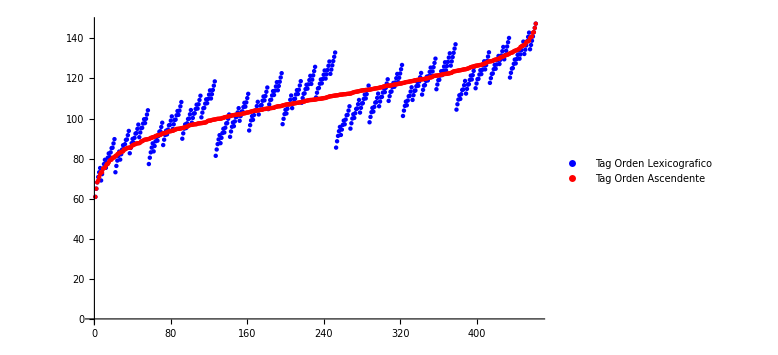

Hamiltoniano con Orden Lexicografico

-Graphics-

Hamiltoniano con Orden de Tag Ascendente

-Graphics-

Energía del Estado Base

(0.02 | -2.96164
0.04 | -2.84649
0.06 | -2.6526
0.08 | -2.38152
0.1 | -2.0487
0.12 | -1.67522
0.14 | -1.27638
0.16 | -0.861076
0.18 | -0.434448
0.2 | 0.000404298
0.22 | 0.441484
0.24 | 0.887435
0.26 | 1.33729
0.28 | 1.79035
0.3 | 2.24608
0.32 | 2.70406
0.34 | 3.16396
0.36 | 3.62553
0.38 | 4.08854
0.4 | 4.55282
0.42 | 5.01822
0.44 | 5.48462
0.46 | 5.95192
0.48 | 6.42001
0.5 | 6.88883
0.52 | 7.3583
0.54 | 7.82836
0.56 | 8.29897
0.58 | 8.77008
0.6 | 9.24165
0.62 | 9.71364
0.64 | 10.186
0.66 | 10.6587
0.68 | 11.1318
0.7 | 11.6052
0.72 | 12.0789
0.74 | 12.5528
0.76 | 13.027
0.78 | 13.5014
0.8 | 13.9761)

Fluctuaciones  Δ(n_i)^2

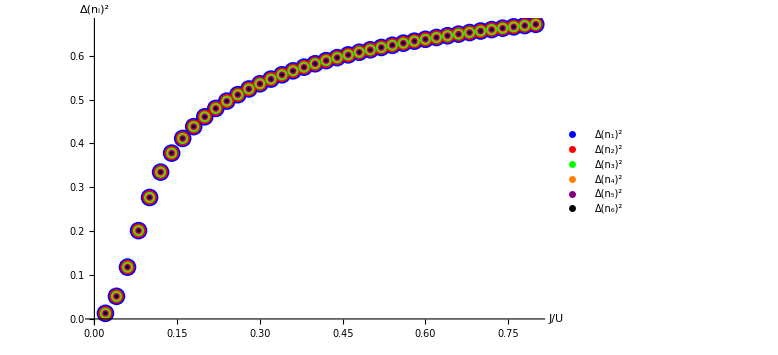

Matriz de Densidad Reducida  ρ. Su traza es igual al numero de partículas

6.

(1. | 0.557918 | 0.456946 | 0.458626 | 0.460212 | 0.459646
0.557918 | 1. | 0.598436 | 0.589848 | 0.58343 | 0.576741
0.456946 | 0.598436 | 1. | 0.662181 | 0.644276 | 0.62721
0.458626 | 0.589848 | 0.662181 | 1. | 0.666971 | 0.63848
0.460212 | 0.58343 | 0.644276 | 0.666971 | 1. | 0.651997
0.459646 | 0.576741 | 0.62721 | 0.63848 | 0.651997 | 1.)

Fracción de Condensado  f_c

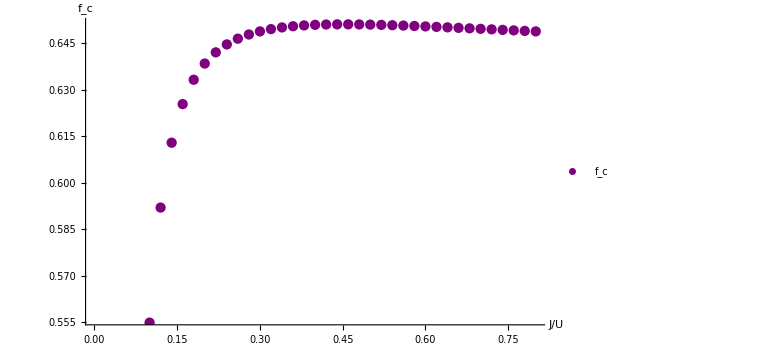

```mathematica
Clear["Global`*"]

(********************* ----- SISTEMA ----- *********************)


(* Se plantea un sistema de M sitios con N Particulas *)

NParticulas=6;
MSitios=6;
NTotalEstados=(NParticulas+MSitios-1)!/((NParticulas)!*(MSitios-1)!);   (*Numero Total de Estados que constituyen la base del espacio de Hilbert *)


(*Parametros*)
U=1.;
t0=0.02;

NPuntos=40.;
t=Table[t0*i,{i,1,NPuntos}];

(*Valores por determinar dentro de las iteraciones*)
EnergiaEdoBase  = Table[ {t[[lk]]    ,     0      }, {lk,1,NPuntos}];   
Dn2  = Table[ {t[[lk]]    ,     0      }, {lk,1,NPuntos}]; 
FraccionCondensado = Table[ {t[[lk]]    ,     0      }, {lk,1,NPuntos}];   




(********************* ----- GENERACIÓN BASE CON ORDEN LEXICOGRAFICO ----- *********************)


(*Funciones para la generación de la base*)
Generadorkn[x_,y_]:=Module[{MSitios=x,in=y},{i=MSitios-1,While[B[[in,i]]==0,i--],kn=i}];       (* Funcion que genera el valor kn de un estado B[[ in ]] para contruir el estado B[[ in+1 ]] *)

GeneradorElemento[x_,y_,z_]:=Module[{MSitios=x,in=y,k=z},{For[i=1,i<k,i++,B[[in+1,i]]=B[[in,i]]],For[i=k,i<k+1,i++,B[[in+1,i]]=B[[in,i]]-1], For[i=k+1,i<k+2,i++,B[[in+1,i]]=NParticulas-Sum[B[[in+1,j]],{j,1,i,1}]],
For[i=k+2,i<MSitios,i++,B[[in+1,i]]=0]}];       (* Funcion que genera el estado B[[ in+1 ]] a partir de el valor kn y del estado B[[ in ]] *)

GeneradorBase[x_,y_]:=Module[{MSitios=x,NTotalEstados=y},Do[{Generadorkn[MSitios,j],GeneradorElemento[MSitios,j,kn]},{j,1,NTotalEstados-1,1}]];  (* Se juntan las dos funciones anteriores iterandolas en un Do, partiendo de un estado inicial para contruir toda la base con orden Lexicografico *)



(***** Se Genera la Base *****)

B=Table[Table[0,{i,1,MSitios}],{i,1,NTotalEstados}];
B[[1,1]]=NParticulas;

GeneradorBase[MSitios,NTotalEstados];
MatrixForm[B];






(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)






(********************* ----- GENERACIÓN DEL TAG-BASE CON ORDEN ASCENDENTE ----- *********************)


TagBase=Table[0,{i,1,NTotalEstados}];
Do[TagBase[[j]]=Sum[Sqrt[100*i+3]*B[[j,i]],{i,1,MSitios,1}],{j,1,NTotalEstados,1}];       (* Se crea un tag para cada estado base a partir de numeros (etiquetas) irrepetibles contruidos por el numero de particulas en cada sitio para cada estado de la base *)
TagBaseOrdenada=Sort[TagBase,#1<#2&];   (* Se ordena de Forma Ascendente *)






(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)




(*ITERACIÓN RESPECTO A t*)
Do[

(********************* ----- HAMILTONIANO CON ORDEN LEXICOGRAFICO ----- *********************)


HBbase=Table[Table[0,{i,1,NTotalEstados,1}],{j,1,NTotalEstados,1}];


(* Terminos No Diagonales *)

Do[{
(*Genero los Operadores como vectores que suman la unidad en un sitio y lo quitan en otro*)
Operador  =  Join[    Table[   UnitVector[MSitios,  Mod[i,MSitios,1]  ]  -   UnitVector[MSitios,  Mod[i+1,MSitios,1]  ],{i,1,MSitios,1}]    ,    Table[  -  UnitVector[MSitios,  Mod[i,MSitios,1]  ]  +   UnitVector[MSitios,  Mod[i+1,MSitios,1]  ],{i,1,MSitios,1}]    ]          ;

(*Aplico cada Operador a un estado*)
EdoOperado  =  Table[  B[[  ln  ]]  +  Operador[[i]]  ,  {i,1,2*MSitios,1} ]          ;

(*Calculo el Tag del estado resultante de cada operación *)
TagEdoOperado  =  Table[  Sum[  Sqrt[  100*i+3  ]  *  EdoOperado[[j,i]]  ,  {i,1,MSitios,1}]  ,  {j,1,2*MSitios,1} ]          ;

(*Calculo el coeficiente asociado a cada operación. El coeficiente esta es el respectivo a los operadores de creación y aniquilación*)
CoefOperador  =  Join[    Table[    Sqrt[  B[[   ln   ,Mod[i,MSitios,1]  ]]  +  1  ]  *  Sqrt[  B[[  ln   ,Mod[i+1,MSitios,1]  ]]  ],{ i,1,MSitios,1}]    ,     Table[        Sqrt[  B[[  ln   ,Mod[i,MSitios,1]  ]]  ]  *   Sqrt[  B[[   ln   ,Mod[i+1,MSitios,1]  ]]  +  1  ] ,{ i,1,MSitios,1}]     ]          ;

(* Identifico la posición del estado resultante de la operación en la Base. Teniendo esto, puedo asignarle el coeficiente a la entrada que corresponde del hamiltoniano *)
Do[   HBbase[[  ln  ,   Flatten[Position[TagBase,TagEdoOperado[[i]]  ]]   ]]      =    HBbase[[  ln  ,   Flatten[Position[TagBase,TagEdoOperado[[i]]  ]]   ]]    +    CoefOperador[[i]]    , {i,1,2*MSitios,1}  ]        },

(*Se itera para todos los estados*)
                                            {ln,1,NTotalEstados,1}];


HBbase  =-t[[     itn    ]]*(HBbase+ConjugateTranspose[HBbase]);    


(* Terminos de la Diagonal *)

HBbaseDiagonal=Table[   Sum[  B[[j,i]]^2  ,{i,1,MSitios,1}  ]  ,{j,1,NTotalEstados}];      (*Respectivo al operador de numero al cuadrado*)

Do[HBbase[[i,i]]=U*HBbaseDiagonal[[i]]/2,{i,1,NTotalEstados}];



HBbase // MatrixForm;







(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)








(********************* ----- HAMILTONIANO CON ORDEN TAG ASCENDENTE ----- *********************)


HTAGbase=Table[Table[0,{i,1,NTotalEstados,1}],{j,1,NTotalEstados,1}];


(*Genero Base REORDENADA respecto al ordenamiento del Tag*)
BOrdenTag=Table[  { TagBase[[j]]  ,  B[[j]]  }  ,{j,1,NTotalEstados}];
BOrdenTag =Sort[  BOrdenTag  ,#1[[1]]<#2[[1]]&] ;       (*Reordena respecto a la primer entrada de los vectores. De menor a mayor*)
BOrdenTag =BOrdenTag[[1;;NTotalEstados,2]];



(* Terminos No Diagonales *)

Do[{
(*Genero los Operadores como vectores que suman la unidad en un sitio y lo quitan en otro*)
Operador  =  Join[    Table[   UnitVector[MSitios,  Mod[i,MSitios,1]  ]  -   UnitVector[MSitios,  Mod[i+1,MSitios,1]  ]     ,{i,1,MSitios,1}]    ,    Table[  -  UnitVector[MSitios,  Mod[i,MSitios,1]  ]  +   UnitVector[MSitios,  Mod[i+1,MSitios,1]  ]     ,{i,1,MSitios,1}]    ]          ;

(*Aplico cada Operador a un estado*)
EdoOperado  =  Table[  BOrdenTag[[  ln  ]]  +  Operador[[i]]  ,  {i,1,2*MSitios,1} ]          ;

(*Calculo el Tag del estado resultante de cada operación *)
TagEdoOperado  =  Table[  Sum[  Sqrt[  100*i+3  ]  *  EdoOperado[[j,i]]  ,  {i,1,MSitios,1}]  ,  {j,1,2*MSitios,1} ]          ;

(*Calculo el coeficiente asociado a cada operación. El coeficiente esta es el respectivo a los operadores de creación y aniquilación*)
CoefOperador  =  Join[    Table[    Sqrt[  BOrdenTag[[   ln   ,Mod[i,MSitios,1]  ]]  +  1  ]  *  Sqrt[  BOrdenTag[[  ln   ,Mod[i+1,MSitios,1]  ]]  ],{ i,1,MSitios,1}]    ,     Table[        Sqrt[  BOrdenTag[[  ln   ,Mod[i,MSitios,1]  ]]  ]  *   Sqrt[  BOrdenTag[[   ln   ,Mod[i+1,MSitios,1]  ]]  +  1  ] ,{ i,1,MSitios,1}]     ]          ;

(* Identifico la posición del estado resultante de la operación en la Base. Teniendo esto, puedo asignarle el coeficiente a la entrada que corresponde del hamiltoniano *)
Do[   HTAGbase[[  ln  ,   Flatten[Position[TagBaseOrdenada,TagEdoOperado[[i]]  ]]   ]]      =    HBbase[[  ln  ,   Flatten[Position[TagBaseOrdenada,TagEdoOperado[[i]]  ]]   ]]    +    CoefOperador[[i]]    , {i,1,2*MSitios,1}  ]        },

(*Se itera para todos los estados*)
                                            {ln,1,NTotalEstados,1}];


HTAGbase  =-t[[     NPuntos    ]] * (HTAGbase+ConjugateTranspose[HTAGbase]);

(* Terminos de la Diagonal *)

Do[HTAGbase[[i,i]]=  U  *   Sum[  BOrdenTag[[i,j]]^2  ,  {j,1,MSitios,1}  ]  /2  ,{i,1,NTotalEstados}];       (*Respectivo al operador de numero al cuadrado*)




HTAGbase // MatrixForm;







(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)







(********************* ----- OBSERVABLES ----- *********************)





(******* ESTADO BASE *******) 



EnergiaEdoBase[[     itn     ,2]]= Eigensystem[-HBbase,1,Method->{"Arnoldi","Criteria"->"RealPart"}][[1]] -  0*U*NParticulas/2 ;      (* Se resta el termino constante del Hamiltoniano *)



EdoBase=Flatten[    Eigensystem[  -HBbase,1,Method->{"Arnoldi","Criteria"->"RealPart"}  ][[2]]    ];





(******* FLUCTUACIONES *******) 


(*La varianza del operador de numero por sitio respecto al estado Base*)

Dn2 [[     itn     , 2 ]] =   Table[      Sum[    B[[i,j]]^2  *  EdoBase[[i]]*  Conjugate[ EdoBase[[i]] ]    ,{i,1,NTotalEstados,1}   ]   -   Sum[    B[[i,j]]  *  EdoBase[[i]]*  Conjugate[ EdoBase[[i]] ]    ,{i,1,NTotalEstados,1}   ]^2    , {j,1,MSitios,1} ];






(******* MATRIZ DE DENSIDAD REDUCIDA *******) 


Mρ=Table[Table[0,{i,1,MSitios,1}],{j,1,MSitios,1}];


(* Terminos No Diagonales *)

(* Operadores y los indices de su entrada correspondiente: Se definen los operadores como vectores para ser sumados al estado sobre el cual actuan. 
Cada operador va a estar asociado a una entrada especifica de la matriz, se considera las entradas de los elementos superiores a la diagonal.*)
Operador  =   Flatten[      Table[  Table[   UnitVector[MSitios,  Mod[j,MSitios,1]  ]  -   UnitVector[MSitios,  Mod[i+j,MSitios,1]  ]     ,{i,1,MSitios-j,1}  ] ,{j,1,MSitios-1,1}   ]    ,1  ]    ;
IndiceFila = Flatten[  Table[   Table[   j  ,{i,j,MSitios-1,1}]   ,{j,1,MSitios-1,1}]  ];
IndiceColumna = Flatten[  Table[   Table[   i  ,{i,j,MSitios,1}]   ,{j,2,MSitios,1}]  ];



Do[    {   

CoefOperadorMρ =Table[0,{i,1,NTotalEstados,1}];

Do[    {

(*Se aplica el operador*)
EdoOperado  =    B[[  ln  ]]  +  Operador [[jn]]     ;

(* Calculo el Tag del estado resultante de cada operación *)
TagEdoOperado  =    Sum[  Sqrt[  100*i+3  ]  *  EdoOperado[[i]]  ,  {i,1,MSitios,1}]    ;

(* Calculo el coeficiente asociado a cada operación. El coeficiente esta es el respectivo a los operadores de creación y aniquilación, PERO ESTA MULTIPLICADO POR EL COEFICIENTE DEL ESTADO PREVIO A SER OPERADO, POR EL COEFICIENTE ASOCIADO AL ESTADO RESULTANTE DE LA OPERACIÓN, i.e., C_{i} * C_{k} donde k es determinado comparando el TAG del EDO OPERADO con la base ordenada, en este caso, la TagBaseORdenada *)
CoefOperadorMρ[[ln]]  =    EdoBase[[    Flatten[  Position[ TagBase,TagEdoOperado ]  ]    ]]  *  Conjugate[ EdoBase[[ ln ]] ]  *  Sqrt[   B[[ ln  ,2 ]]  +  1  ]  *  Sqrt[  B[[ ln  ,1 ]]   ]       }

      ,   {ln,1,NTotalEstados,1}   ]            ;
 

CoefOperadorMρ = Flatten [CoefOperadorMρ ]            ;   (*Posiciones no encontradas asigna elementos vacios {} que impiden sumar y multiplicar adecuadamente*)

(* Se asigna el elemento de la matriz como la suma de todos los coeficientes de cada estado operado *)
Mρ[[  IndiceFila[[jn]]  ,  IndiceColumna[[jn]]  ]]=  Sum[  CoefOperadorMρ [[i]]  , {i,1,Length[CoefOperadorMρ ],1}  ]                                  }
         
(* Se itera para todos los operadores, i.e., todos los elementos superiores a la diagonal *)
                                ,{jn,1,MSitios(MSitios-1)/2,1}] ;



   Mρ=Mρ+ConjugateTranspose[Mρ];




(* Terminos de la Diagonal *)

Do[  Mρ[[j,j]]=   Sum[    B[[i,j]]  *  EdoBase[[i]]*  Conjugate[ EdoBase[[i]] ]    ,{i,1,NTotalEstados,1}   ]   ,   {j,1,MSitios,1}   ];       (*Respectivo al operador de numero al cuadrado*)      



Mρ // MatrixForm ;







(******* FRACCIÓN DE CONDENSADO *******) 

FraccionCondensado[[     itn     , 2 ]] =Max[   Eigensystem[   Mρ   ,MSitios][[1]]  ]   /  NParticulas   ;
(* Puede ser Max[  Eigensystem[Mρ,MSitios,Method->{"Arnoldi","Criteria"->"RealPart"}][[1]]  ] *)








, {itn,1,NPuntos,1}];  (*ITERACIÓN RESPECTO A t*)


(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------------------------------------------------------------------------------------*)







(********************* ----- OUTPUTS DEL CODIGO ----- *********************)


(* Para evitar las iteraciones respecto a t *)
(* No todos los datos se guardan para cada caso de t, como los hamiltnoanianos, Matriz de Densidad Reducida, por lo que vemos sólo los correspondientes a la ultima iteración. *)


(******* BASE *******)
MatrixForm[B];
TagBaseOrdenada;   

Print[ Style["Comparación de los Valores de Tags en la Base con orden Lexicografico respecto al orden de Tag Ascendente",18,Bold,Purple]]
ListPlot[{TagBase,TagBaseOrdenada},ImageSize->Large,LabelStyle->{14,Black},PlotStyle->{{Thick,Blue},{Thick,Red}},PlotLegends->{"Tag Orden Lexicografico","Tag Orden Ascendente"}]



(******* HAMILTONIANO CON ORDEN LEXICOGRAFICO *******)
Print[ Style["Hamiltoniano con Orden Lexicografico",18,Bold,Purple]]
HBbase // MatrixForm;
MatrixPlot[HBbase ,PlotTheme->"Detailed",ImageSize->Large,ColorFunction->Hue]



(******* HAMILTONIANO CON ORDEN TAG ASCENDENTE *******)
Print[ Style["Hamiltoniano con Orden de Tag Ascendente",18,Bold,Purple]]
HTAGbase // MatrixForm;
MatrixPlot[HTAGbase  , PlotTheme->"Detailed",ImageSize->Large,ColorFunction->Hue]



(******* ENERGÍA ESTADO BASE *******)
EnergiaEdoBase=Flatten[  EnergiaEdoBase  ];
EnergiaEdoBase=Table[   {EnergiaEdoBase[[i]]  ,  EnergiaEdoBase[[i+1]]}   , {i,1,2*NPuntos,2}];

Print[ Style["Energía del Estado Base",18,Bold,Purple]]
EnergiaEdoBase  //MatrixForm



(******* FLUCTUACIONES *******)
Print[ Style["Fluctuaciones  Δ(n_i)^2",18,Bold,Purple]]
Dn2;

ListPlot[     Table[   Table[   {  Dn2[[lk,1]]  ,  Dn2[[lk,2,jk]]  }   ,{lk,1,NPuntos,1}]   ,{jk,1,MSitios,1}]     ,ImageSize->Large,AxesStyle->{Black,Black},PlotStyle->{{PointSize[0.022],Blue},{PointSize[0.018],Red},{PointSize[0.014],Green},{PointSize[0.011],Orange},{PointSize[0.008],Purple},{PointSize[0.004],Black}},PlotLegends->{"Δ(n_1)^2","Δ(n_2)^2","Δ(n_3)^2","Δ(n_4)^2","Δ(n_5)^2","Δ(n_6)^2"} ,ImageSize->Large,LabelStyle->{14,Black},AxesLabel->{"J/U" ,"Δ(n_i)^2"}]



(******* MATRIZ DE DENSIDAD REDUCIDA *******)
Print[ Style["Matriz de Densidad Reducida  ρ. Su traza es igual al numero de partículas",18,Bold,Purple]];
Tr[Mρ]
Mρ // MatrixForm 
MatrixPlot[Mρ  , PlotTheme->"Detailed",ImageSize->Large,ColorFunction->Hue];



(******* FRACCIÓN DE CONDENSADO *******)
FraccionCondensado=Flatten[  FraccionCondensado  ];
FraccionCondensado=Table[   {FraccionCondensado[[i]]  ,  FraccionCondensado[[i+1]]}   , {i,1,2*NPuntos,2}];

Print[ Style["Fracción de Condensado  f_c",18,Bold,Purple]]
FraccionCondensado;

ListPlot[FraccionCondensado,ImageSize->Large,AxesStyle->{Black,Black},PlotStyle->{Thickness[10],Purple},PlotLegends->{"f_c"} ,ImageSize->Large,LabelStyle->{14,Black},AxesLabel->{"J/U" ,"f_c"}]
```